```mathematica
a[x_] = x + 0.2*Cos[5*x+5]
```

```mathematica
x+0.2 Cos[5+5 x]
```

x+0.2 Cos[5+5 x]

```mathematica
g[y_,x_,z_] = z
```

z

```mathematica
ContourPlot3D[{g[y,x,z]==0,f[y,x,z]==0},{y,0,1},{x,0,1},{z,0,1},MeshFunctions->{Function[{x,y,z,h},f-g]},MeshStyle->{{Thick,Blue}},Mesh->{{0}}]
```

MeshFunctions::invmeshf: MeshFunctions->Function[{x,y,z,h},f-g] must be a pure function or a list of pure functions.

-Graphics3D-

```mathematica
h=-y +a[x];
g=z;
ContourPlot3D[{h==0,g==0},{x,0,1},{y,0,1},{z,0,0.1}, ContourStyle->Directive[Orange,Opacity[0],Specularity[White,0]] , MeshFunctions->{Function[{x,y,z,f},h-g]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Orange,Opacity[0],Specularity[White,0]], AxesLabel->MaTeX@{"t","x"}]
```

-Graphics3D-

```mathematica
f[x_, y_] = 1*Exp[-(y-a[x])^2/0.07]
<<MaTeX`
```

ⅇ^(-14.2857 (-x+y-0.2 Cos[5+5 x])^2)

```mathematica
Plot3D[f[x,y],{x,0,1} ,{y,0,1},AxesLabel->MaTeX@{"t","x","\\rho(x,t)"},MeshFunctions->{Function[{x,y,z,f},h-0.001*z]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},WorkingPrecision->10]
```

-Graphics3D-

```mathematica
PacletInstall
```

PacletInstall

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.9.paclet"]
```

PacletObject[…]

```mathematica
Vreel[x_] = -1/1000*(Cos[2*x]-1)^10;
```

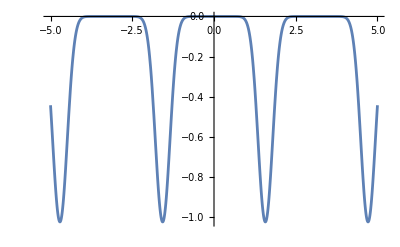

```mathematica
Plot[Vreel[x],{x,-5,5}]
```